```mathematica
极坐标下弹簧摆的轨迹
```

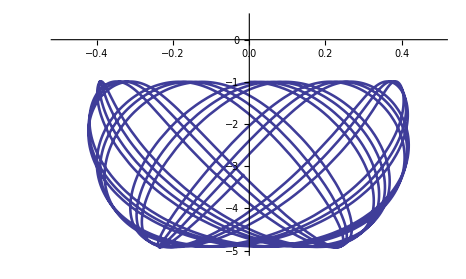

```mathematica
g=9.8;k=0.1;m=0.02;L0=1;tm=50.0;
θinitial={0,0.5/L0};
Linitial={L0,0};
equs=
{L[t] θ''[t]==-2L'[t] θ'[t]-g Sin[θ[t]],
L''[t]==-k/m (L[t]-L0)+g Cos[θ[t]]+L[t] θ'[t]^2,
θ[0]==θinitial[[1]],θ'[0]==θinitial[[2]],
L[0]==Linitial[[1]],L'[0]==Linitial[[2]]};
s=NDSolve[equs,{θ,L},{t,0,tm},MaxSteps->∞];
{θ,L}={θ,L}/.s[[1]];
ParametricPlot[{L[t]*Sin[θ[t]],-L[t]*Cos[θ[t]]},
{t,0,tm},PlotRange->{{-0.5,0.5},{-5,0.5}},
AspectRatio->0.6,PlotStyle->Thickness[0.004],
AxesStyle->Thickness[0.003]]
Clear[g,k,s,m,L0,tm,equs,θ,L]
```